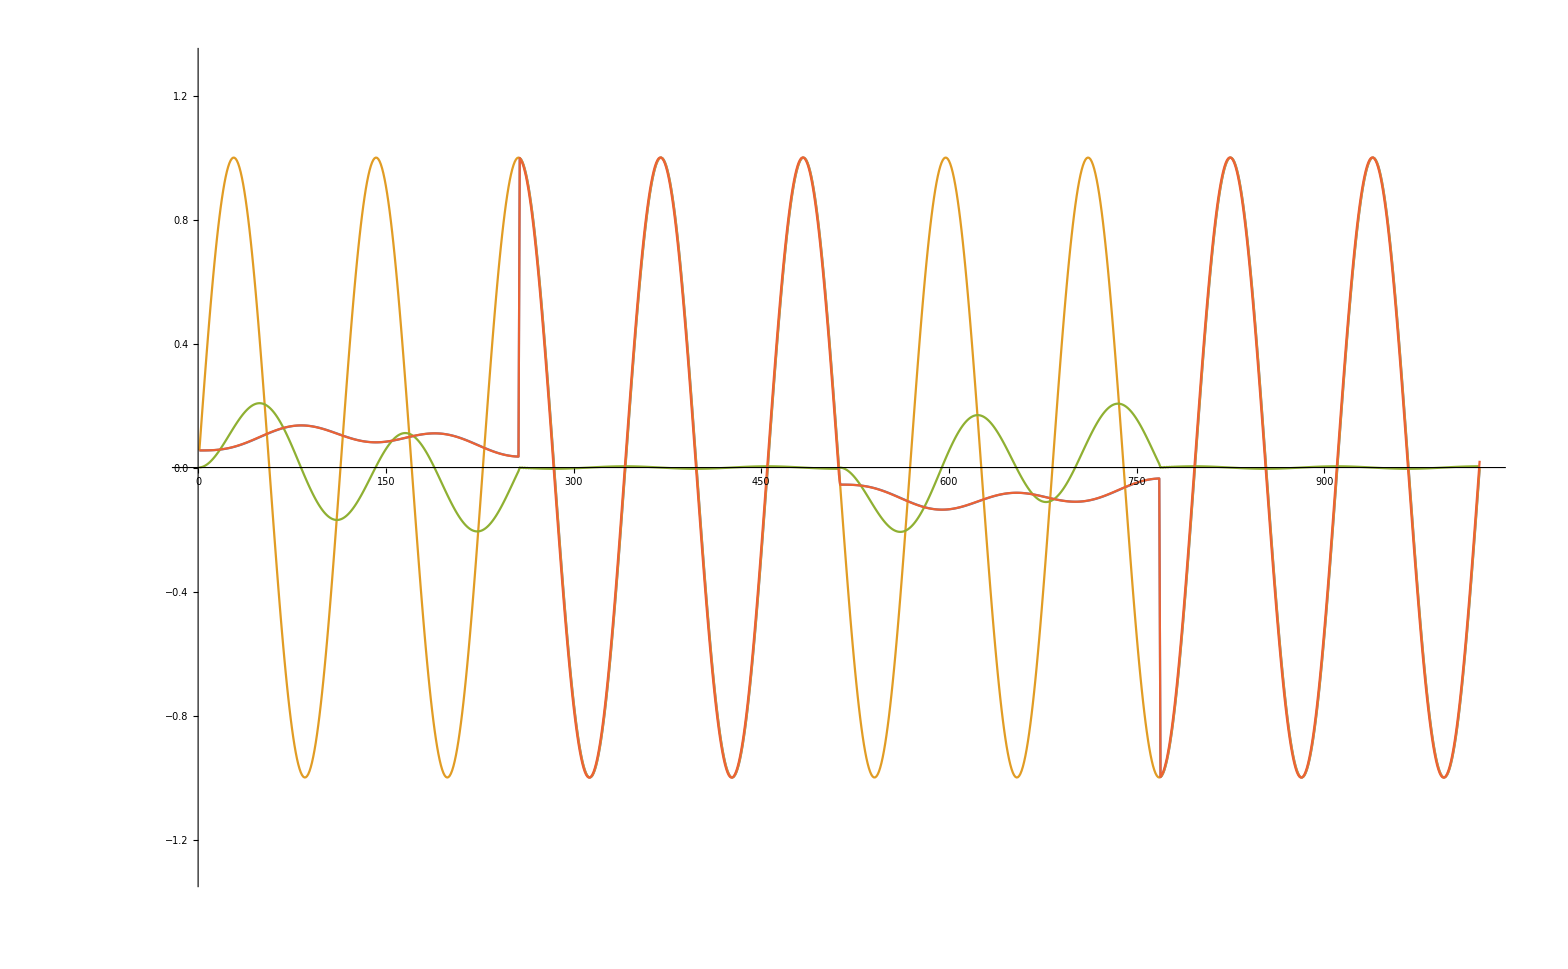

```mathematica
a1=0;
a2=0;
a3=0;
ic1 = 0;
ic2 = 0;
lastX = 0;
lastXX = 0;
lastY = 0;
lastYY = 0;

setFcAndQHard[fc_,Q_]:=Module[{g=Tan[π fc / 2],k = 1/Q},
a1= 1/(1+g*(g+k));
a2= g*a1;
a3=g*a2;
]

setFcAndQSoft[fc_,Q_,x_]:=Module[{g=Tan[π fc / 2],k = 1/Q},
a1= 1/(1+g*(g+k));
a2= g*a1;
a3=g*a2;

ic1=(x-lastX)*a2;
ic2 = x;
]

simperSVFLowpass[x_]:=Module[{v1, v2, v3},
v3 = x-ic2;
v1= a1*ic1 +a2*v3;
v2 = ic2 + a2*ic1 + a3*v3;

ic1 = 2*v1 - ic1;
ic2 = 2*v2 - ic2;

lastXX = lastX;
lastX = x;
lastYY = lastY;
lastY = v2;

{v2,x,ic1,ic2}
]

testLength = 1024;
input = Sin[#]& /@ (9 2 π Range[testLength]/testLength);

lf = N[60/22050];
hf = N[20000/22050];
setFcAndQSoft[lf,Sqrt[1/2],input[[1]]]
outputA =simperSVFLowpass/@input[[1;;testLength/4]];
setFcAndQSoft[hf,Sqrt[1/2],input[[1+testLength/4]]]
outputB =simperSVFLowpass/@input[[1+testLength/4;;2testLength/4]];
setFcAndQSoft[lf,Sqrt[1/2],input[[1+2testLength/4]]]
outputC =simperSVFLowpass/@input[[1+2testLength/4;;3testLength/4]];
setFcAndQSoft[hf,Sqrt[1/2],input[[1+3testLength/4]]]
outputD =simperSVFLowpass/@input[[1+3testLength/4;;testLength]];
output = Join[outputA,outputB,outputC,outputD];
ListLinePlot[Transpose[output],PlotRange->1.3{-1,1}]
```

## Feedback Compressor Tests

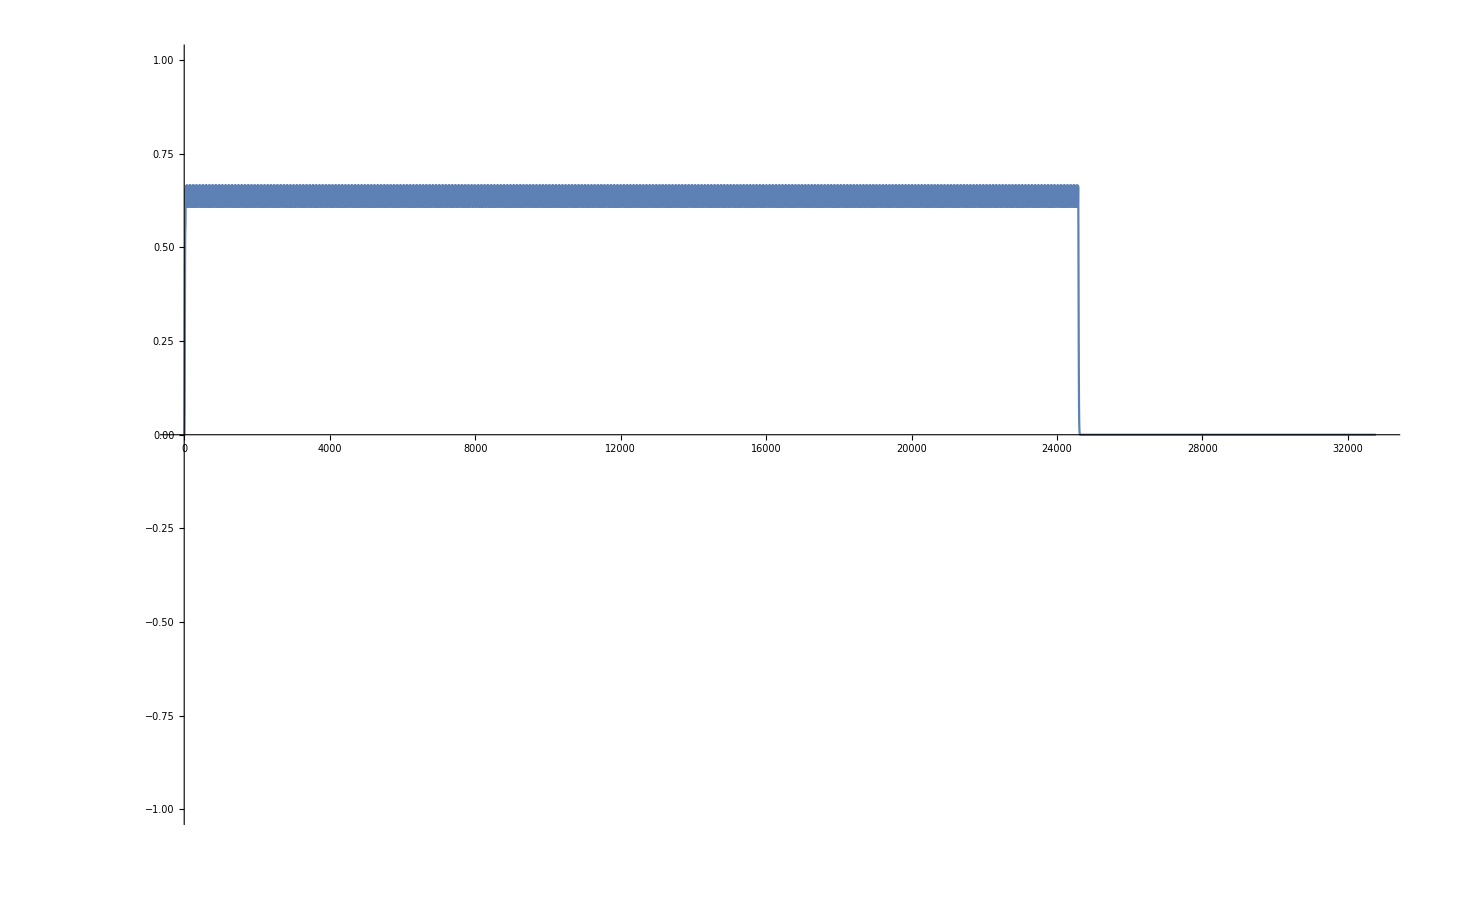

```mathematica
compInputGain = 1.0;
compThreshold = 0.1;
compQ = 0.5;
prevEnvelope = 0.0;
attackFreq =N[200/22050];
aaFreq =N[2000/22050];
releaseFreq = N[10/22050];

a1=0;
a2=0;
a3=0;
ic1 = 0;
ic2 = 0;
lastX = 0;
lastXX = 0;
lastY = 0;
lastYY = 0;

testLength = 2^15;
input = Sin[#]& /@ (900 2 π Range[testLength]/testLength);

input[[-2^13;;All]]=0;

compressorSVFLowpass[x_]:=Module[{v1, v2, v3},
v3 = x-ic2;
v1= a1*ic1 +a2*v3;
v2 = ic2 + a2*ic1 + a3*v3;

ic1 = 2*v1 - ic1;
ic2 = 2*v2 - ic2;

lastXX = lastX;
lastX = x;
lastYY = lastY;
lastY = v2;

v2
]

(* anti-aliasing filters *)
ic11 = 0;
ic21 = 0;
a1s=0;
a2s =0;
compressorSVFLowpass1[x_]:=Module[{v1, v2, v3},
v3 = x-ic21;
v1= a1s*ic11 +a2s*v3;
v2 = ic21 + a2s*ic11 + a3s*v3;

ic11 = 2*v1 - ic11;
ic21 = 2*v2 - ic21;

v2
]
ic12 = 0;
ic22 = 0;
compressorSVFLowpass2[x_]:=Module[{v1, v2, v3},
v3 = x-ic22;
v1= a1s*ic12 +a2s*v3;
v2 = ic22 + a2s*ic12 + a3s*v3;

ic12 = 2*v1 - ic12;
ic22 = 2*v2 - ic22;

v2
]
ic13 = 0;
ic23 = 0;
compressorSVFLowpass3[x_]:=Module[{v1, v2, v3},
v3 = x-ic23;
v1= a1s*ic13 +a2s*v3;
v2 = ic23 + a2s*ic13 + a3s*v3;

ic13 = 2*v1 - ic13;
ic23 = 2*v2 - ic23;

v2
]

setFcAndQAAFilters[fc_,Q_]:=Module[{g=Tan[π fc / 2],k = 1/Q},
a1s= 1/(1+g*(g+k));
a2s= g*a1s;
a3s=g*a2s;
]

feedbackCompressor[x_]:=Module[{output, envelope,attenuation=1.0,filterFreq},
(* apply the input gain *)
output = x*compInputGain;


(* rectify the input *)
envelope = Abs[x];

(* apply antialiasing filters to rectified input *)
envelope=compressorSVFLowpass3[compressorSVFLowpass2[compressorSVFLowpass1[envelope]]];

(* lowpass filter the rectified input *)
(*envelope=compressorSVFLowpass[envelope];*)

(* find the attenuation that would bring the volume back to unity *)
If[envelope >0,attenuation = compThreshold / envelope,attenuation=1.0];

(* don't allow the attenuation to increase the volume; reduce only *)
If[attenuation > 1.0,attenuation = 1.0];

(* set the compressor input gain *)
compInputGain = attenuation;

(* set the filter frequency to attack or release *)
If[envelope > prevEnvelope,filterFreq =attackFreq, filterFreq =releaseFreq];
setFcAndQHard[filterFreq,compQ];

(* save the previous envelope value *)
prevEnvelope = envelope;

(* output *)
envelope
]

setFcAndQHard[releaseFreq,compQ];
setFcAndQAAFilters[aaFreq,compQ];
ListLinePlot[feedbackCompressor/@input,PlotRange->{-1,1}]
```